# Reduced approach

```mathematica
ClearAll[ϕ,ψ,ψ0,A,B,B0,M,InvM,RHS,DynSis,phiPrime,psiPrime,APrime,BPrime,Da,Db,dA,dB,p,b,m,s,DynSis,DynSisV2,DynSisV3,DynSisV4,FastSlowEq];
F[A_,B_]:=-dA*A+m*B+2*p*A*B
G[A_,B_]:=B*(-dB-m-2*p*A+2*b-2*b*(A+B))
M[A_,B_]:={{Da*(1-B)+p*B,Da*A,0,0},{Db*B,Db*(1-A)-b*(A+B),0,0},{0,0,1,0},{0,0,0,1}}
(*Vector on the right-hand side*)
RHS[A_,B_]:={-s*ϕ-F[A,B],-s*ψ-G[A,B],ϕ,ψ};
(*order replacer*)
Da = ϵ;
Db = ϵ;
dA = ϵ^2;
dB = ϵ^2;
m = ϵ^3;
p = 2*ϵ;
s = b;
(*Inverted left-hand side matrix*)
InvM[A_,B_] := Inverse[M[A,B]];
(*Isolating derivatives on the right hand-side {phiPrime,psiPrime,APrime,BPrime}*)
DynSis := FullSimplify[InvM[A,B].RHS[A,B]]
DynSis //MatrixForm
Eq:= DynSis == {0,0,0,0}
equi= Solve[Eq,{ϕ,ψ,A,B}];
NonTrivialEq = FullSimplify[equi[[2]]];
(* Extract expressions for A and B *)
Aexpr = A /. NonTrivialEq;
Bexpr = B /. NonTrivialEq;
```

((A^2 ϵ (ϵ^2+b (-2 B+ϵ))-(b B-ϵ) (B ϵ^3+b ϕ)-A (ϵ^2 (ϵ-B (4+ϵ))+b^2 ϕ+b ϵ (B (2+2 B+(-1+ϵ) ϵ)+ϕ+ψ)))/(ϵ (b (1+B) (A+B)+(-1+A-B+2 A B) ϵ))
(-B (ϵ (A (4+8 B-ϵ)+ϵ (1+B+ϵ+2 B ϵ))+b (2 (1+B) (-1+A+B)+ϕ))+b (1+B) ψ)/(b (1+B) (A+B)+(-1+A-B+2 A B) ϵ)
ϕ
ψ)

```mathematica
B = (ϵ)*B0;
A = 1 * A0;
ψ = (ϵ)*ψ0;
DynSisV2 = FullSimplify[InvM[A,B].RHS[A,B]];
SimpDynSisV2 = FullSimplify[MapAt[#/(ϵ) &, DynSisV2, {{2}}]];
SimpDynSisV2 = FullSimplify[MapAt[#/1 &, SimpDynSisV2, {{3}}]];
SimpDynSisV2 = FullSimplify[MapAt[#/(ϵ) &, SimpDynSisV2, {{4}}]];
Series[SimpDynSisV2,{ϵ,0,1}] //MatrixForm
```

(-(b ϕ)/ϵ+b B0 ϕ+(A0-2 B0-2 A0 B0+B0 ϕ-b B0^2 ϕ-ψ0) ϵ+O[ϵ]^2
(2 B0-2 A0 B0-B0 ϕ+ψ0)/A0+((2 B0-4 A0 B0-2 A0^2 B0-2 b B0^2-B0 ϕ+A0 B0 ϕ+b B0^2 ϕ+A0 b B0^2 ϕ+ψ0-A0 ψ0-b B0 ψ0) ϵ)/(A0^2 b)+O[ϵ]^2
ϕ
ψ0)

```mathematica
Clear[SimpEquiV2];
SimpEqV2 := SimpDynSisV2 == {0,0,0,0};
SimpEquiV2 = FullSimplify[Solve[SimpEqV2,{ϕ,ψ0,A0,B0}]];
NonTrivialA0 = A0 /. SimpEquiV2[[2]];
NonTrivialA0
NonTrivialB0 = B0 /. SimpEquiV2[[2]];
NonTrivialB0
```

(-2 ϵ^2 (1+2 ϵ)-b (-4+ϵ+ϵ^2)+√(4 ϵ^4+4 b ϵ^2 (-4+ϵ+ϵ^2)+b^2 (16+ϵ (-8+ϵ (9+ϵ (2+ϵ))))))/(8 (b+2 ϵ))

-(2 ϵ^2-b (4+ϵ+ϵ^2)+√(4 ϵ^4+4 b ϵ^2 (-4+ϵ+ϵ^2)+b^2 (16+ϵ (-8+ϵ (9+ϵ (2+ϵ))))))/(8 b ϵ)

(5.68029 | -24.7572 | 180.194 | -39.204
-6628.81 | 27033.4 | -363792. | 42288.6
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

(X'[t]==5.68029 X[t]-24.7572 Y[t]+180.194 Z1[t]-39.204 Z2[t]
Y'[t]==-6628.81 X[t]+27033.4 Y[t]-363792. Z1[t]+42288.6 Z2[t]
Z1'[t]==X[t]
Z2'[t]==Y[t]
X[0]==X0
Y[0]==Y0
Z1[0]==Z10
Z2[0]==Z20)

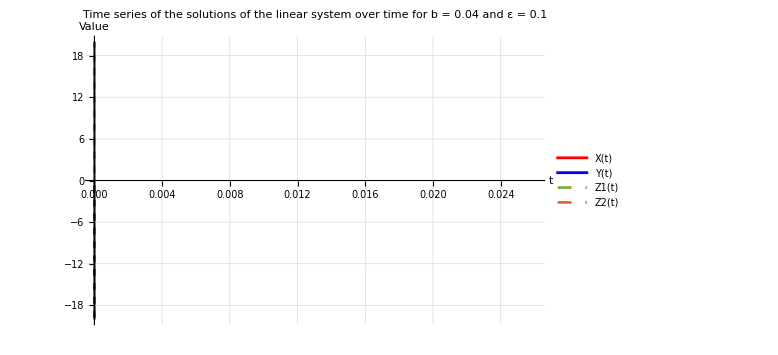

Eigenvalues at non-trivial equilibrium of the linearization

(27041.1+0. ⅈ
-0.180957+12.3712 ⅈ
-0.180957-12.3712 ⅈ
-1.60456+0. ⅈ)

Eigenvalues at trivial equilibrium of the linearizaation

(-0.2+0.806226 ⅈ
-0.2-0.806226 ⅈ
-0.574166+0. ⅈ
0.174166+0. ⅈ)

```mathematica
(*Construct the Jacobian of the Multivariate Taylor Expansion*)
ClearAll[CutJacobian]
Series[D[SimpDynSisV2,{{ϕ,ψ0,A0,B0}}],{ϵ,0,3}];
CutJacobian = Normal[%] /. {A0 -> NonTrivialA0, B0 -> NonTrivialB0, ϕ -> 0 , ψ0 -> 0};
(*IMPORTANT PARAMETER CHANGING*)
b0 = 0.04;
ϵ0 = 0.1;
(*Construct the rest of the linear simulation*)
CutJacobianTrivial = D[SimpDynSisV2,{{ϕ,ψ0,A0,B0}}] /. {A0 -> 0, B0 -> 0, ϕ -> 0, ψ0 -> 0};
ReplacedCutJacobian = CutJacobian /. {ϵ->ϵ0, b->b0};
ReplacedCutJacobianTrivial = CutJacobianTrivial /. {ϵ->ϵ0, b->b0};
ReplacedCutJacobian //MatrixForm;
ReplacedCutJacobian //MatrixForm
vars = {X[t], Y[t], Z1[t], Z2[t]};
(* Construct ODE system *)
full = (ReplacedCutJacobian.vars);
eqns = Join[
  Thread[D[vars, t] == full],
  {X[0] == X0, Y[0] == Y0, Z1[0] == Z10, Z2[0] == Z20}
];
eqns //MatrixForm
(* Solve the system *)
sol = DSolve[eqns, vars, t];
Xres = X[t] /. sol[[1]];
Yres = Y[t] /. sol[[1]];
Z1res = Z1[t] /. sol[[1]];
Z2res = Z2[t] /. sol[[1]];
NumRep = {X0 -> 0, Y0 -> 0, Z10 -> NonTrivialA0 /. {ϵ -> ϵ0, b -> b0} , Z20 -> NonTrivialB0 /. {ϵ -> ϵ0, b -> b0}};
{Xsol[t_], Ysol[t_], Z1sol[t_], Z2sol[t_]} = {X[t], Y[t], Z1[t], Z2[t]} /. sol[[1]] /. NumRep;
Plot[
  {Xsol[t], Ysol[t], Z1sol[t], Z2sol[t]},
  {t, 0, 100},
  PlotLegends -> {"X(t)", "Y(t)", "Z1(t)", "Z2(t)"},
  PlotStyle -> {Red, Blue, Dashed, Dashed},
  PlotRange -> {-20,20},
  AxesLabel -> {"t", "Value"},
  GridLines -> Automatic,
  ImageSize -> Large,
  PlotLabel -> Row[{"Time series of the solutions of the linear system over time for b = ",b0," and ε = ",ϵ0}]
]
Row[{"Eigenvalues at non-trivial equilibrium of the linearization"}]
Eigenvalues[ReplacedCutJacobian] //MatrixForm
Row[{"Eigenvalues at trivial equilibrium of the linearizaation"}]
Eigenvalues[ReplacedCutJacobianTrivial] //MatrixForm
```